#### Kyle Cranmer’s Problems Day 1

#### Problem 1: The Poisson Model

```mathematica
Pois[n_,ν_]:=(Exp[-ν] ν^n)/(n!)
```

(a)

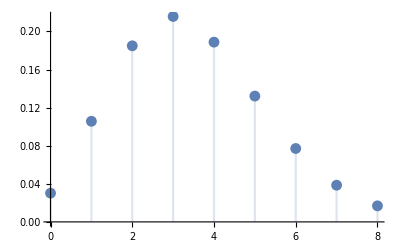

```mathematica
DiscretePlot[Pois[n,3.5],{n,0,8}]
```

Because the right-tail has values to the infinity, the distribution has a peak at the integer before ν i.e., n=3.

(b)

```mathematica
LogL[n_,ν_]=-ν+n Log[ν]-Log[n!]
```

-ν+n Log[ν]-Log[n!]

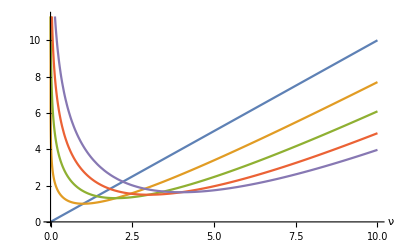

```mathematica
Plot[-LogL[#,ν]&/@{0,1,2,3,4}//Evaluate,{ν,0,10},AxesLabel->{"ν"}]
```

This shows the likelihood on the true value of ν. Because information available is only n, the most likely value of ν is n.

(c)

```mathematica
D[-LogL[n,ν],ν]==0
Solve[%,ν]
```

1-n/ν==0

{{ν→n}}

(d)

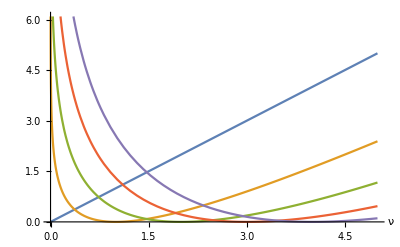

```mathematica
Plot[-LogL[n,ν]+LogL[n,n]/.{{n->0.00001},{n->1},{n->2},{n->3},{n->4}}//Evaluate,{ν,0,5},
AxesLabel->{"ν"}]
```

Note that ν̂ maximizes L[ν]. Thus L[ν̂]is the maximum of L, and -ln(L[ν]/L[ν̂])is always non-negative, and with peak at ν=ν̂ (=n) with a value of 0.

(e)

```mathematica
DiscretePlot[Pois[n,3.5],{n,0,8}]
```

-Graphics-

This is exactly same as that of (a). ν̂ is always integer.

(f)

```mathematica
-LogL[n,3.5]+LogL[n,n]/.{{n->0.0000001},{n->1},{n->2},{n->3},{n->4}}
```

{3.5,1.24724,0.380768,0.037548,0.0341256}

(g)

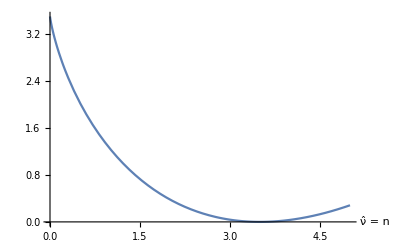

```mathematica
Plot[-LogL[n,3.5]+LogL[n,n],{n,0,5},AxesLabel->{"ν̂ = n"}]
```

This shows what value of ν̂, i.e., what value of n will be observed.
Note that the value at ν̂=3 is smaller, i.e., more probable, than that at ν̂=4.

```mathematica
{Exp[-LogL[n,3.5]+LogL[n,n]/.n->3]/Exp[-LogL[n,3.5]+LogL[n,n]/.n->4],Pois[3,3.5]/Pois[4,3.5]}
```

{1.00343,1.14286}

The value at ν̂ which is not integer is meaningless.

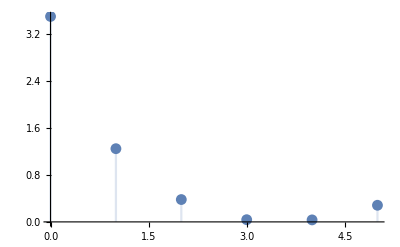

```mathematica
DiscretePlot[-LogL[n,3.5]+LogL[n,n],{n,{0.00001,1,2,3,4,5}},AxesLabel->{"ν̂ = n"}]
```

#### Problem 2: A simple signal and background model

```mathematica
Pois[n,ϵ νs+νb]
```

(ⅇ^(-νb-ϵ νs) (νb+ϵ νs)^n)/(n!)

```mathematica
LogL[n_,ϵ_,νs_,νb_]:=-νb-ϵ νs+n Log[νb+νs ϵ]-Log[n!]
Solve[D[-LogL[n,ϵ,νs,νb],νs]==0,νs]
```

{{νs→(n-νb)/ϵ}}

Where I assumed νb and ϵ are known.
(Otherwise it is not determined.)

#### Problem 3: A two-bin example

```mathematica
LogL[n1_,ϵ1_,νs_,νb1_,n2_,ϵ2_,νb2_]:=-νb1-ϵ1 νs+n1 Log[νb1+νs ϵ1]-Log[n1!]-νb2-ϵ2 νs+n2 Log[νb2+νs ϵ2]-Log[n2!]
```

(a)

```mathematica
EQ=D[-LogL[n1,ϵ1,νs,νb1,n2,ϵ2,νb2],νs]==0
```

ϵ1+ϵ2-(n1 ϵ1)/(νb1+ϵ1 νs)-(n2 ϵ2)/(νb2+ϵ2 νs)==0

(b)

```mathematica
Solve[EQ/.{νb1->0,νb2->0},νs]
```

{{νs→(n1+n2)/(ϵ1+ϵ2)}}

Interesting that this is not n1/ϵ1+n2/ϵ2, but this is, with a thought, obvious...

(c)
In this case, an excess/deficit in Exp2 is with good belief considered as an excess/deficit from background events. So Exp2 will be ignored and mostly independent on n2.
MLE will be asymptotically n1/ϵ1.
This can be checked by taking the limit of νb2→∞:

```mathematica
νshat=1/(2 (ϵ1^2 ϵ2+ϵ1 ϵ2^2))(n1 ϵ1 ϵ2+n2 ϵ1 ϵ2-ϵ1 ϵ2 νb1-ϵ2^2 νb1-ϵ1^2 νb2-ϵ1 ϵ2 νb2+√((-n1 ϵ1 ϵ2-n2 ϵ1 ϵ2+ϵ1 ϵ2 νb1+ϵ2^2 νb1+ϵ1^2 νb2+ϵ1 ϵ2 νb2)^2-4 (ϵ1^2 ϵ2+ϵ1 ϵ2^2) (-n2 ϵ2 νb1-n1 ϵ1 νb2+ϵ1 νb1 νb2+ϵ2 νb1 νb2)));
Series[νshat,{νb2,∞,1}]//FullSimplify[#,{ϵ1>0,ϵ2>0}]&//Normal//Collect[#,{n1,n2},Simplify]&
```

-νb1/ϵ1+n1 (1/(ϵ1+ϵ2)+(n2 ϵ2)/((ϵ1+ϵ2)^2 νb2))